HZ prescription interpolated calculation.

## Write Data to files.

Preparing

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica

154

Test Legend fuctioning.

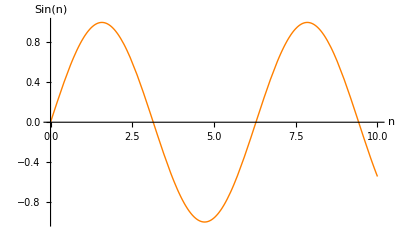

```mathematica
(*********************************************)
Print[Style["Preparing",Orange]]
(*********************************************)
Needs["PlotLegends`"]
SetDirectory["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\"]
(*********************************************)
(*Manually set the start point(a<1) of this table.*)
tranzs=tranzL=tranzDE2=tranzDE3=tranzDE4=47;
(*Manually set the criteria for the element in aokTabL etc that corresponds to normalization time.*)
nort=201-tranzL
(**************************)
Print[Style["Test Legend fuctioning.",Orange]]
Plot[Sin[n],{n,0,10},PlotStyle->Orange,AxesLabel-> {"n","Sin(n)"},PlotLegend->{"Sin"},LegendPosition->{1.1,-0.4}]
```

```mathematica
(*********************************************)
Print[Style["Parameters",Orange]]
(*********************************************)
 w1 =-1;
 w2 =-0.1;
 w3 =-0.5;
 w4 =-4/5;
 ΩDE0 =0.73;
Ωk0=0;
 Ωm0 =0.27;
 Ωr0 =8.09*10^-5;
h=0.71;
(*h=1;*)
 (*H0 =(100 h)/300000;*)
H0=100 h/300000;
Ωm0s =1; 
Ωr0s =8.09*10^-5*(1/1.2)^2;
(*Ωr0s=0;*)
aeq=Ωr0/Ωm0
```

Parameters

0.00029963

```mathematica
(*********************************************)
Print[Style["Intial conditions for Hubble constant, normalized at early time",Orange]]
(*********************************************)
HL0=H20=H30=H40=H0;
Hs0=H0*1.2;
```

Intial conditions for Hubble constant, normalized at early time

```mathematica
(*********************************************)
Print[Style["Define Hubble functions",Orange]]
(*********************************************)
Hs[a_]:=2 Hs0  √(Ωm0s a^-3+ Ωr0s a^-4);
HL[a_]:=2 HL0  √(Ωm0 a^-3+ Ωr0 a^-4+ ΩDE0 a^(-3(1+w1)))
H2[a_]:=2 H20 √(Ωm0 a^-3+ Ωr0 a^-4+ ΩDE0 a^(-3(1+w2)))
H3[a_]:=2 H30 √(Ωm0 a^-3+ Ωr0 a^-4+ ΩDE0 a^(-3(1+w3)))
H4[a_]:=2 H40 √(Ωm0 a^-3+ Ωr0 a^-4+ ΩDE0 a^(-3(1+w4)))
```

Define Hubble functions

```mathematica
(*(*********************************************)
Print[Style["Hubble distances",Orange]]
(*********************************************)
dHL[a]=1/HL[a];dH2[a]=1/H2[a];dH3[a]=1/H3[a];dH4[a]=1/H4[a];*)
```

```mathematica
(*********************************************)
Print[Style["Define k of a",Orange]]
(*********************************************)
kL[a_]= HL[a];ks[a_]= Hs[a];kDE2[a_]= H2[a];kDE3[a_]= H3[a];kDE4[a_]= H4[a];
keq=HL[aeq]/h
k0=HL[1]/h
(*ss[k_]:=NSolve[k==Subscript[H, 1][Subscript[a, 1]]&&Subscript[a, 1]>0,Subscript[a, 1]]//FullSimplify
Solve[k== H2[a2],a2];*)
```

Define k of a

94.4558

0.000666694

```mathematica
(*********************************************)
Print[Style["Define growth factors",Orange]]
(*********************************************)
Growths[a_]:= 5/2 Ωm0s  Hs[a]/Hs0 NIntegrate[1/(x^3(Hs[x]/Hs0)^3),{x,0,a}];
GrowthL[a_]:= 5/2 Ωm0  HL[a]/HL0 NIntegrate[1/(x^3(HL[x]/HL0)^3),{x,0,a}];
GrowthDE2[a_]:=5/2 Ωm0  H2[a]/H20  NIntegrate[1/(x^3(H2[x]/H20)^3),{x,0,a}];
GrowthDE3[a_]:=5/2 Ωm0  H3[a]/H30  NIntegrate[1/(x^3(H3[x]/H30)^3),{x,0,a}];
GrowthDE4[a_]:=5/2 Ωm0  H4[a]/H40  NIntegrate[1/(x^3(H4[x]/H40)^3),{x,0,a}];
```

Define growth factors

Plot k of a

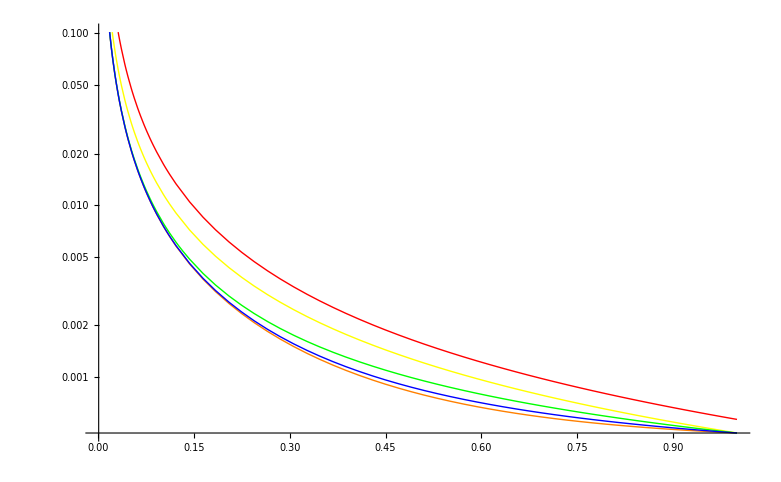

```mathematica
(*********************************************)
Print[Style["Plot k of a",Orange]]
(*********************************************)
LogPlot[{ks[a],kL[a],kDE2[a],kDE3[a],kDE4[a]},{a,10^-3,1},PlotStyle->{Red,Orange,Yellow,Green,Blue}]
```

Plot growth factors of a for LCDM

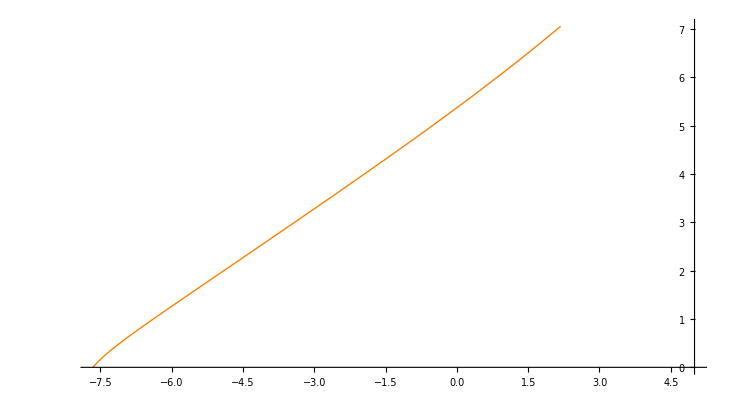

```mathematica
(*********************************************)
Print[Style["Plot growth factors of a for LCDM",Orange]]
(*********************************************)
ParametricPlot[{Log[kL[a]],Log[GrowthL[1]/GrowthL[a]]},{a,10^-3,1},PlotRange->Full,AxesOrigin-> {5,0},PlotStyle->{Orange}]
```

Plot growth factors of a for all models

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.7194}. NIntegrate obtained 5.3194  + 17.2853\ ⅈ
 and 14.0762 for the integral and error estimates.

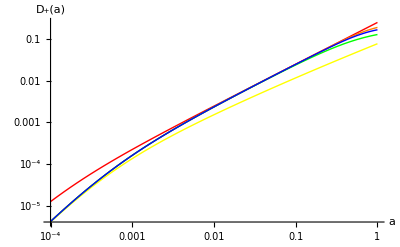

```mathematica
(*********************************************)
Print[Style["Plot growth factors of a for all models",Orange]]
(*********************************************)
Plot[{Growths[a],GrowthL[a],GrowthDE2[a],GrowthDE3[a],GrowthDE4[a]},{a,0,1},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {a,"D_+(a)"}];
LogLogPlot[{Growths[a],GrowthL[a],GrowthDE2[a],GrowthDE3[a],GrowthDE4[a]},{a,10^-4,1},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {a,"D_+(a)"},PlotLegend->{"sCDM", "LCDM","DE2","DE3","DE4"},LegendPosition->{1.1,-0.4}]
```

```mathematica
(*********************************************)
Print[Style["Tranform growth factors / Hubble distances of a to those of 1+z",Orange]]
(*********************************************)
GS[mn_]:=Growths[1/mn];GL[mn_]:=GrowthL[1/mn];GDE2[mn_]:=GrowthDE2[1/mn];GDE3[mn_]:=GrowthDE3[1/mn];GDE4[mn_]:=GrowthDE4[1/mn];
Lambdas[mn_]=1/Hs[1/mn];LambdaL[mn_]=1/HL[1/mn];Lambda2[mn_]=1/H2[1/mn];Lambda3[mn_]=1/H3[1/mn];Lambda4[mn_]=1/H4[1/mn];
```

Tranform growth factors / Hubble distances of a to those of 1+z

Plot Hubble distances

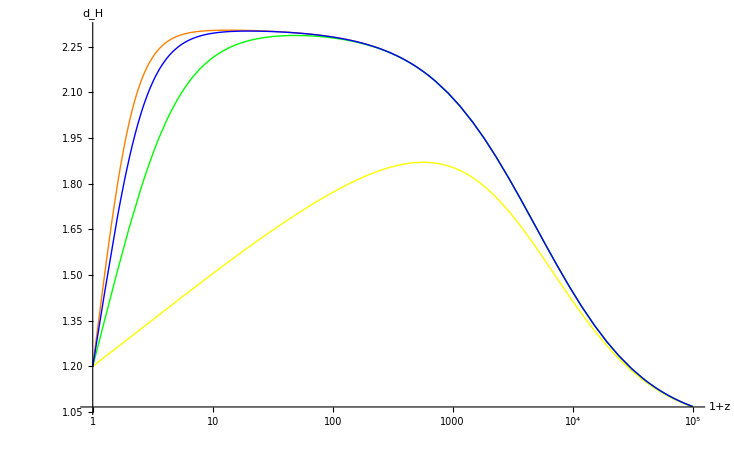

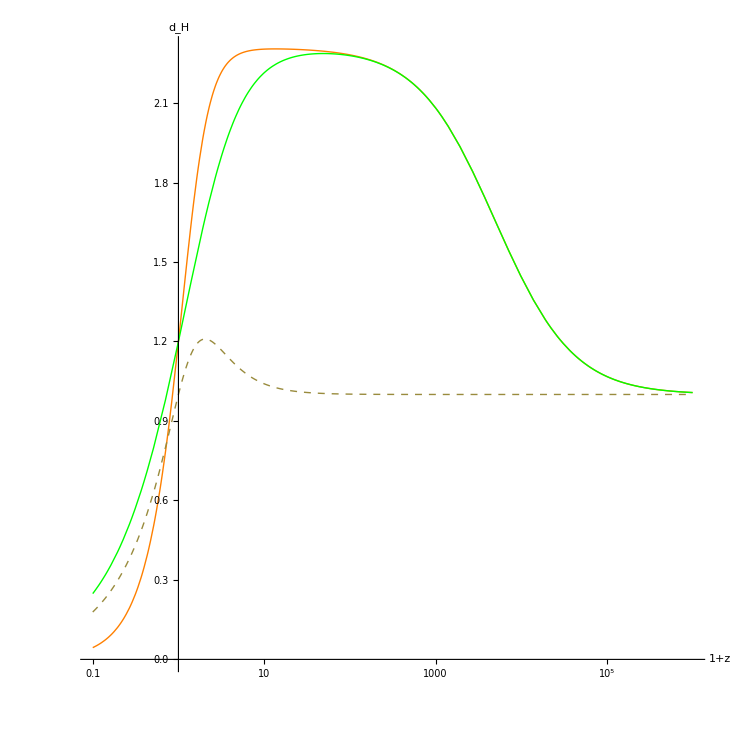

LogPlot::exclul: {Im[e] - 0, Im[e] - 0, Im[e^3\ mn + 0.0000561806\ e^4\ mn] - 0, Im[e] - 0, Im[e] - 0, Im[0.27\ e^3\ mn + 0.0000809\ e^4\ mn] - 0} must be a list of equalities or real-valued functions.

LogPlot::exclul: {Im[e] - 0, Im[e] - 0, Im[e^3\ mn + 0.0000561806\ e^4\ mn] - 0, Im[e] - 0, Im[e] - 0, Im[e] - 0, Im[e^-mn] - 0, Im[0.27\ e^3\ mn + 0.0000809\ e^4\ mn + 0.73/(e^Times[« 2 »])^1.5] - 0} must be a list of equalities or real-valued functions.

LogPlot::exclul: {Im[e] - 0, Im[e] - 0, Im[0.27\ e^3\ mn + 0.0000809\ e^4\ mn] - 0, Im[e] - 0, Im[e] - 0, Im[e] - 0, Im[e^-mn] - 0, Im[0.27\ e^3\ mn + 0.0000809\ e^4\ mn + 0.73/(e^Times[« 2 »])^1.5] - 0} must be a list of equalities or real-valued functions.

General::stop: Further output of LogPlot :: exclul will be suppressed during this calculation.

-Graphics-

```mathematica
(*********************************************)
Print[Style["Plot Hubble distances",Orange]]
(*********************************************)
LogLinearPlot[{LambdaL[mn]/Lambdas[mn],Lambda2[mn]/Lambdas[mn],Lambda3[mn]/Lambdas[mn],Lambda4[mn]/Lambdas[mn]},{mn,1,10^5},PlotStyle->{Orange,Yellow,Green,Blue},AxesLabel->{"1+z","d_H"}]
LogLinearPlot[{LambdaL[mn]/Lambdas[mn],Lambda3[mn]/Lambdas[mn],LambdaL[mn]/Lambda3[mn]},{mn,0.1,10^6},PlotStyle->{Orange,Green,Dashed},AxesLabel->{"1+z","d_H"},AxesOrigin-> {1,0},AspectRatio->1]
LogPlot[{LambdaL[e^mn]/Lambdas[e^mn],Lambda3[e^mn]/Lambdas[e^mn],LambdaL[e^mn]/Lambda3[e^mn]},{mn,0.1,10^6},PlotStyle->{Orange,Green,Dashed},AxesLabel->{"1+z","d_H"},AxesOrigin-> {1,0},AspectRatio->1]
```

Plot growth factors in terms of 1+z

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

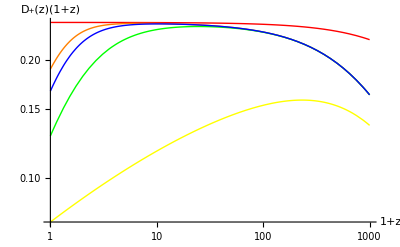

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

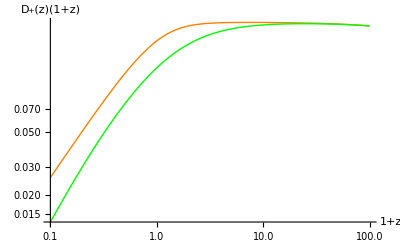

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

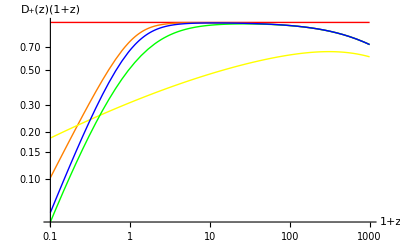

```mathematica
(*********************************************)
Print[Style["Plot growth factors in terms of 1+z",Orange]]
(*********************************************)
LogLogPlot[{(mn)GS[mn],(mn)GL[mn],(mn)GDE2[mn],(mn)GDE3[mn],(mn)GDE4[mn]},{mn,1,1000},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {"1+z","D_+(z)(1+z)"},PlotLegend->{"sCDM","LCDM","DE2","DE3","DE4"},LegendPosition->{1.1,-0.4}]
LogLogPlot[{(mn)GL[mn],(mn)GDE3[mn]},{mn,0.1,100},PlotStyle->{Orange,Green},AxesLabel-> {"1+z","D_+(z)(1+z)"},PlotLegend->{"LCDM","DE3"},LegendPosition->{1.1,-0.4}]
(*Another normalization*)
LogLogPlot[{GS[mn]/GS[mn],GL[mn]/GS[mn],GDE2[mn]/GS[mn],GDE3[mn]/GS[mn],GDE4[mn]/GS[mn]},{mn,0.1,1000},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {"1+z","D_+(z)(1+z)"},PlotLegend->{"sCDM","LCDM","DE2","DE3","DE4"},LegendPosition->{1.1,-0.4}]
(*LogLogPlot[{1,GL[mn]/GS[mn],GDE2[mn]/GS[mn],GDE3[mn]/GS[mn],GDE4[mn]/GS[mn]},{mn,0.1,100},AxesLabel-> {"1+z","D_+(z)(1+z)"}]*)
```

Import power spectrum of LCDM calculated by cmbeasy, and some test

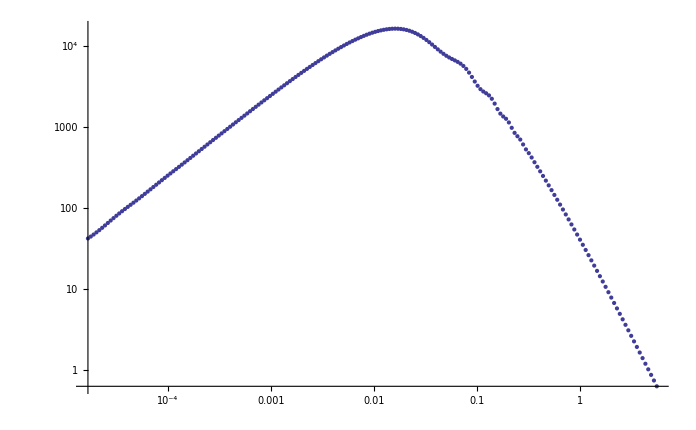

0.0000167287

0.000312121

774.957

201

0.0000118774==0.000473333 √(0.73+0.0000809/aL^4+0.27/aL^3)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{aL→-0.717923},{aL→-0.00029963}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{aL→-0.717923},{aL→-0.00029963}}

```mathematica
(*********************************************)
Print[Style["Import power spectrum of LCDM calculated by cmbeasy, and some test",Orange]]
(*********************************************)
PowerS=Import["cdm_11-27.dat"];
ListLogLogPlot[PowerS]
PowerS[[1,1]]
PowerS[[tranzs]][[1]]
PowerS[[tranzs]][[2]]
leth=Length[PowerS]
PowerS[[1,1]]h== HL[aL]
Solve[PowerS[[1,1]]h== HL[aL],aL,Reals]
NSolve[PowerS[[1,1]]h== HL[aL],aL,Reals]
```

```mathematica
(*********************************************)
Print[Style["Tests for Hubble equations",Orange]]
(*********************************************)
HL[1]/h
HL[0.01]/h
HL[0.001]/h
HL[0.0001]/h
HL[0.00001]/h
HL[0.000001]/h
```

Tests for Hubble equations

0.000666694

0.351562

12.4882

692.499

60955.4

6.00629×10^6

```mathematica
(*********************************************)
Print[Style["Create tables for power spectrums, and test",Orange]]
(*********************************************)
(*Manually set the start point(a≤1) of this table.*)(*Moved to the beginning of the file.*)
(*tranzs=43;tranzL=43;tranzDE2=43;tranzDE3=43;tranzDE4=43;*)
(********)
(*PowerS[[100]][[1]]== HL[L]
Solve[(PowerS[[115]][[1]])^2 L^4== L^4(HL[L])^2,L]
LogLogPlot[{L^4(Hs[L])^2,L^4(HL[L])^2,L^4(H2[L])^2,L^4(H3[L])^2,L^4(H4[L])^2,(PowerS[[115]][[1]])^2 L^4},{L,0.00001,100000},PlotStyle->{Red,Orange,Yellow,Green,Blue,Black}]*)
aokTabs=Table[as/.NSolve[(PowerS[[i,1]]h)^2 as^4==as^4(Hs[as])^2&&as>0,as,Reals],{i,tranzs+1,leth}];
aokTabL=Table[aL/.NSolve[(PowerS[[i,1]]h)^2 aL^4==aL^4(HL[aL])^2&&aL>0,aL,Reals],{i,tranzL+1,leth}];
aokTabDE2=Table[a2/.NSolve[(PowerS[[i,1]]h)^2 a2^4==a2^4(H2[a2])^2&&a2>0,a2,Reals],{i,tranzDE2+1,leth}];
aokTabDE3=Table[a3/.NSolve[(PowerS[[i,1]]h)^2 a3^4==a3^4(H3[a3])^2&&a3>0,a3,Reals],{i,tranzDE3+1,leth}];
aokTabDE4=Table[a4/.NSolve[(PowerS[[i,1]]h)^2 a4^4==a4^4(H4[a4])^2&&a4>0,a4,Reals],{i,tranzDE4+1,leth}];
aokTabs[[1]]
Length[aokTabL]
aokTabs
aokTabL
aokTabDE2
aokTabDE3
aokTabDE4
```

Create tables for power spectrums, and test

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

{1.79514}

154

{{1.79514},{1.7206},{1.64915},{1.58068},{1.51504},{1.45214},{1.39184},{1.33405},{1.27865},{1.22556},{1.17467},{1.1259},{1.07915},{1.03434},{0.991392},{0.950227},{0.910772},{0.872955},{0.836708},{0.801966},{0.768667},{0.73675},{0.706159},{0.676838},{0.648735},{0.621798},{0.59598},{0.571234},{0.547515},{0.524782},{0.502992},{0.482107},{0.462089},{0.442903},{0.424513},{0.406887},{0.389992},{0.3738},{0.358279},{0.343403},{0.329145},{0.315479},{0.30238},{0.289825},{0.277791},{0.266257},{0.255202},{0.244606},{0.23445},{0.224716},{0.215386},{0.206443},{0.197872},{0.189657},{0.181782},{0.174235},{0.167001},{0.160067},{0.153422},{0.147052},{0.140947},{0.135095},{0.129486},{0.12411},{0.118958},{0.114019},{0.109285},{0.104748},{0.1004},{0.0962315},{0.0922365},{0.0884073},{0.0847372},{0.0812194},{0.0778477},{0.074616},{0.0715185},{0.0685497},{0.065704},{0.0629766},{0.0603624},{0.0578568},{0.0554552},{0.0531533},{0.050947},{0.0488323},{0.0468054},{0.0448627},{0.0430006},{0.0412159},{0.0395053},{0.0378657},{0.0362942},{0.0347879},{0.0333442},{0.0319604},{0.0306341},{0.0293628},{0.0281444},{0.0269765},{0.0258572},{0.0247843},{0.0237559},{0.0227703},{0.0218256},{0.0209201},{0.0200522},{0.0192204},{0.018423},{0.0176588},{0.0169264},{0.0162243},{0.0155514},{0.0149064},{0.0142883},{0.0136957},{0.0131278},{0.0125835},{0.0120618},{0.0115617},{0.0110824},{0.010623},{0.0101827},{0.00976062},{0.0093561},{0.00896838},{0.00859676},{0.00824057},{0.00789917},{0.00757194},{0.0072583},{0.00695769},{0.00666955},{0.00639338},{0.00612868},{0.00587497},{0.00563179},{0.00539871},{0.0051753},{0.00496118},{0.00475594},{0.00455922},{0.00437068},{0.00418996},{0.00401674},{0.00385072},{0.00369159},{0.00353906},{0.00339287},{0.00325275},{0.00311845},{0.00298972},{0.00286634},{0.00274807}}

{aL,aL,aL,aL,aL,aL,aL,aL,aL,{1.72833},{1.19452},{0.989241},{0.86599},{0.779007},{0.712137},{0.657936},{0.612401},{0.573149},{0.538657},{0.507894},{0.480134},{0.454849},{0.431641},{0.410204},{0.390298},{0.371734},{0.354356},{0.338036},{0.322669},{0.308166},{0.29445},{0.281458},{0.269131},{0.257422},{0.246286},{0.235686},{0.225587},{0.215958},{0.206771},{0.198002},{0.189626},{0.181624},{0.173974},{0.16666},{0.159665},{0.152972},{0.146568},{0.140439},{0.134572},{0.128954},{0.123575},{0.118424},{0.113491},{0.108766},{0.104239},{0.0999028},{0.0957484},{0.0917682},{0.0879545},{0.0843004},{0.0807989},{0.0774437},{0.0742284},{0.0711472},{0.0681945},{0.0653648},{0.0626529},{0.0600539},{0.0575631},{0.0551759},{0.052888},{0.0506952},{0.0485937},{0.0465794},{0.044649},{0.0427987},{0.0410254},{0.0393257},{0.0376966},{0.0361352},{0.0346387},{0.0332044},{0.0318296},{0.0305119},{0.029249},{0.0280385},{0.0268783},{0.0257663},{0.0247004},{0.0236788},{0.0226997},{0.0217611},{0.0208616},{0.0199994},{0.019173},{0.018381},{0.0176218},{0.0168941},{0.0161967},{0.0155282},{0.0148874},{0.0142733},{0.0136846},{0.0131204},{0.0125797},{0.0120613},{0.0115645},{0.0110883},{0.0106319},{0.0101944},{0.00977512},{0.00937321},{0.00898798},{0.00861874},{0.00826483},{0.0079256},{0.00760045},{0.00728879},{0.00699007},{0.00670374},{0.00642929},{0.00616622},{0.00591407},{0.00567238},{0.00544072},{0.00521866},{0.00500581},{0.00480179},{0.00460623},{0.00441878},{0.00423909},{0.00406686},{0.00390176},{0.0037435},{0.0035918},{0.00344638},{0.00330698},{0.00317336},{0.00304527},{0.00292248},{0.00280477},{0.00269193},{0.00258375},{0.00248005},{0.00238063},{0.00228532},{0.00219395},{0.00210634},{0.00202236},{0.00194183},{0.00186463},{0.00179061},{0.00171964},{0.00165158}}

{{1.65008},{1.57608},{1.50541},{1.43794},{1.3735},{1.31197},{1.25321},{1.1971},{1.14352},{1.09235},{1.04348},{0.996816},{0.952249},{0.909686},{0.869038},{0.830217},{0.793142},{0.757733},{0.723914},{0.691615},{0.660766},{0.631302},{0.60316},{0.576281},{0.550608},{0.526086},{0.502663},{0.48029},{0.45892},{0.438507},{0.419008},{0.400382},{0.38259},{0.365594},{0.349358},{0.333849},{0.319032},{0.304878},{0.291356},{0.278439},{0.266098},{0.254308},{0.243044},{0.232283},{0.222001},{0.212178},{0.202793},{0.193826},{0.185259},{0.177073},{0.169252},{0.161778},{0.154637},{0.147814},{0.141294},{0.135064},{0.129111},{0.123422},{0.117986},{0.112791},{0.107826},{0.103082},{0.0985487},{0.0942159},{0.0900752},{0.086118},{0.082336},{0.0787215},{0.075267},{0.0719653},{0.0688096},{0.0657935},{0.0629107},{0.0601553},{0.0575216},{0.0550043},{0.052598},{0.0502979},{0.0480993},{0.0459976},{0.0439886},{0.0420681},{0.0402323},{0.0384773},{0.0367995},{0.0351956},{0.0336622},{0.0321963},{0.0307948},{0.0294549},{0.0281739},{0.0269492},{0.0257782},{0.0246586},{0.0235881},{0.0225646},{0.021586},{0.0206502},{0.0197555},{0.0188999},{0.0180818},{0.0172995},{0.0165514},{0.0158361},{0.015152},{0.0144979},{0.0138723},{0.013274},{0.0127019},{0.0121547},{0.0116315},{0.011131},{0.0106524},{0.0101946},{0.00975679},{0.00933804},{0.00893753},{0.00855445},{0.00818805},{0.00783758},{0.00750236},{0.0071817},{0.00687499},{0.00658159},{0.00630094},{0.00603248},{0.00577566},{0.00552998},{0.00529496},{0.00507013},{0.00485504},{0.00464927},{0.00445241},{0.00426407},{0.00408388},{0.00391149},{0.00374654},{0.00358873},{0.00343774},{0.00329326},{0.00315503},{0.00302276},{0.00289619},{0.00277508},{0.00265919},{0.00254829},{0.00244216},{0.0023406},{0.00224341},{0.00215039},{0.00206137},{0.00197618},{0.00189463},{0.00181659}}

{{2.20074},{2.03844},{1.88959},{1.75307},{1.62782},{1.51289},{1.4074},{1.31054},{1.22156},{1.13978},{1.06457},{0.995358},{0.931609},{0.872845},{0.818628},{0.768555},{0.722263},{0.679419},{0.639723},{0.602899},{0.5687},{0.536901},{0.507299},{0.479707},{0.453959},{0.429904},{0.407403},{0.386334},{0.366581},{0.348044},{0.330629},{0.314252},{0.298836},{0.28431},{0.270611},{0.25768},{0.245465},{0.233916},{0.222989},{0.212644},{0.202841},{0.193547},{0.18473},{0.176361},{0.168412},{0.160858},{0.153676},{0.146845},{0.140344},{0.134155},{0.128261},{0.122645},{0.117292},{0.112189},{0.107322},{0.102679},{0.0982476},{0.0940181},{0.08998},{0.0861236},{0.08244},{0.0789207},{0.0755578},{0.0723436},{0.0692711},{0.0663336},{0.0635247},{0.0608383},{0.0582689},{0.0558109},{0.0534593},{0.0512092},{0.0490561},{0.0469955},{0.0450232},{0.0431354},{0.0413282},{0.0395981},{0.0379416},{0.0363556},{0.034837},{0.0333827},{0.03199},{0.0306562},{0.0293787},{0.0281552},{0.0269832},{0.0258606},{0.0247853},{0.0237551},{0.0227683},{0.0218229},{0.0209171},{0.0200493},{0.0192179},{0.0184213},{0.0176581},{0.0169267},{0.016226},{0.0155545},{0.0149111},{0.0142946},{0.0137038},{0.0131377},{0.0125952},{0.0120753},{0.011577},{0.0110996},{0.010642},{0.0102035},{0.0097833},{0.00938056},{0.00899459},{0.00862468},{0.00827016},{0.00793039},{0.00760476},{0.00729266},{0.00699355},{0.00670686},{0.0064321},{0.00616875},{0.00591634},{0.00567442},{0.00544255},{0.00522031},{0.00500729},{0.00480312},{0.00460742},{0.00441985},{0.00424006},{0.00406772},{0.00390253},{0.0037442},{0.00359243},{0.00344694},{0.00330749},{0.00317382},{0.00304568},{0.00292284},{0.0028051},{0.00269222},{0.00258402},{0.00248029},{0.00238084},{0.00228551},{0.00219412},{0.0021065},{0.0020225},{0.00194196},{0.00186474},{0.00179071},{0.00171973},{0.00165166}}

{{6.05721},{4.92548},{4.01786},{3.29324},{2.71807},{2.26454},{1.90898},{1.63102},{1.41328},{1.24145},{1.10421},{0.992943},{0.901283},{0.824563},{0.759375},{0.703223},{0.654254},{0.611082},{0.572652},{0.538154},{0.506955},{0.478555},{0.452555},{0.428631},{0.406521},{0.386006},{0.366905},{0.349067},{0.332362},{0.316681},{0.301928},{0.288023},{0.274894},{0.262479},{0.250723},{0.239578},{0.229},{0.21895},{0.209393},{0.200299},{0.191639},{0.183386},{0.175517},{0.168011},{0.160847},{0.154006},{0.147473},{0.14123},{0.135263},{0.129558},{0.124103},{0.118885},{0.113893},{0.109117},{0.104546},{0.10017},{0.0959819},{0.0919718},{0.0881321},{0.0844552},{0.0809339},{0.0775613},{0.0743309},{0.0712366},{0.0682723},{0.0654325},{0.0627119},{0.0601053},{0.0576078},{0.0552148},{0.0529218},{0.0507247},{0.0486193},{0.0466017},{0.0446684},{0.0428156},{0.04104},{0.0393384},{0.0377077},{0.0361449},{0.0346471},{0.0332117},{0.0318359},{0.0305174},{0.0292538},{0.0280427},{0.0268819},{0.0257694},{0.0247031},{0.0236812},{0.0227017},{0.0217629},{0.0208631},{0.0200008},{0.0191742},{0.018382},{0.0176227},{0.0168949},{0.0161973},{0.0155287},{0.0148879},{0.0142737},{0.013685},{0.0131208},{0.0125799},{0.0120616},{0.0115647},{0.0110885},{0.0106321},{0.0101946},{0.00977524},{0.00937331},{0.00898807},{0.00861882},{0.00826489},{0.00792566},{0.0076005},{0.00728883},{0.0069901},{0.00670377},{0.00642931},{0.00616625},{0.00591409},{0.0056724},{0.00544073},{0.00521868},{0.00500583},{0.0048018},{0.00460624},{0.00441878},{0.0042391},{0.00406686},{0.00390176},{0.0037435},{0.0035918},{0.00344638},{0.00330699},{0.00317336},{0.00304527},{0.00292248},{0.00280477},{0.00269193},{0.00258375},{0.00248005},{0.00238063},{0.00228532},{0.00219395},{0.00210634},{0.00202236},{0.00194183},{0.00186463},{0.00179061},{0.00171964},{0.00165158}}

```mathematica
(*********************************************)
Print[Style["Export aok table",Orange]]
(*********************************************)
Export["DEs\\Sync\\aokTabs.xls",aokTabs,"XLS"]
Export["DEs\\Sync\\aokTabL.xls",aokTabL,"XLS"]
Export["DEs\\Sync\\aokTabDE2.xls",aokTabDE2,"XLS"]
Export["DEs\\Sync\\aokTabDE3.xls",aokTabDE3,"XLS"]
Export["DEs\\Sync\\aokTabDE4.xls",aokTabDE4,"XLS"]
```

Export aok table

DEs\Sync\aokTabs.xls

DEs\Sync\aokTabL.xls

DEs\Sync\aokTabDE2.xls

DEs\Sync\aokTabDE3.xls

DEs\Sync\aokTabDE4.xls

```mathematica
(*********************************************)
Print[Style["Normalization factors. normalized to a early time of about a=10^-3",Orange]]
(*********************************************)
(*Manually set the criteria for the element in aokTabL etc that corresponds to normalization time.*)
(*nort=197-tranzL*)
fracs=1/((Growths[1]/Growths[aokTabs[[nort]][[1]]])/(GrowthL[1]/GrowthL[aokTabL[[nort]][[1]]]))
frac2=1/((GrowthDE2[1]/GrowthDE2[aokTabDE2[[nort]][[1]]])/(GrowthL[1]/GrowthL[aokTabL[[nort]][[1]]]))
frac3=1/((GrowthDE3[1]/GrowthDE3[aokTabDE3[[nort]][[1]]])/(GrowthL[1]/GrowthL[aokTabL[[nort]][[1]]]))
frac4=1/((GrowthDE4[1]/GrowthDE4[aokTabDE4[[nort]][[1]]])/(GrowthL[1]/GrowthL[aokTabL[[nort]][[1]]]))
(*frac2=1;frac3=1;frac4=1;*)
```

Normalization factors. normalized to a early time of about a=10^-3

1.6157

2.17368

1.48189

1.138

```mathematica
(*********************************************)
Print[Style["Tables for Q factors",Orange]]
(*********************************************)
Qfactor2=Table[{PowerS[[i+tranzDE2,1]],frac2 (GrowthDE2[1]/GrowthDE2[aokTabDE2[[i]][[1]]])/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]])},{i,1,leth-tranzDE2}];
Qfactor3=Table[{PowerS[[i+tranzDE3,1]],frac3 (GrowthDE3[1]/GrowthDE3[aokTabDE3[[i]][[1]]])/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]])},{i,1,leth-tranzDE3}];
Qfactor4=Table[{PowerS[[i+tranzDE4,1]],frac4 (GrowthDE4[1]/GrowthDE4[aokTabDE4[[i]][[1]]])/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]])},{i,1,leth-tranzDE4}];
Qfactor2Ex=Table[{PowerS[[i,1]],frac2},{i,1,tranzDE2}];
Qfactor3Ex=Table[{PowerS[[i,1]],frac3},{i,1,tranzDE3}];
Qfactor4Ex=Table[{PowerS[[i,1]],frac4},{i,1,tranzDE4}];
Qfac2=Join[Qfactor2Ex,Qfactor2];
Qfac3=Join[Qfactor3Ex,Qfactor3];
Qfac4=Join[Qfactor4Ex,Qfactor4];
Qfactor2[[1]]
Qfactor2[[1]][[1]]
(*********************************************)
Print[Style["Export the Q factors",Orange]]
(*********************************************)
Export["DEs\\Sync\\QfactorDE2vsL.xls",Qfac2,"XLS"]
Export["DEs\\Sync\\QfactorDE3vsL.xls",Qfac3,"XLS"]
Export["DEs\\Sync\\QfactorDE4vsL.xls",Qfac4,"XLS"]
```

Tables for Q factors

Part::partd: Part specification aL ⟦ 1 ⟧ is longer than depth of object.

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

Part::partd: Part specification aL ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification aL ⟦ 1 ⟧ is longer than depth of object.

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

Part::partd: Part specification aL ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification aL ⟦ 1 ⟧ is longer than depth of object.

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

Part::partd: Part specification aL ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{0.000332622,10.4087 NIntegrate[1/(x^3 (HL[x]/HL0)^3),{x,0,aL⟦1⟧}] √(0.73+0.0000809/aL⟦1⟧^4+0.27/aL⟦1⟧^3)}

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

0.000332622

Export the Q factors

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

DEs\Sync\QfactorDE2vsL.xls

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

DEs\Sync\QfactorDE3vsL.xls

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

DEs\Sync\QfactorDE4vsL.xls

Power spectrums for the models. This is a slow method to calculate the power spectrums but it's steady.

Construct the normalized power spectrum (different units) and export them

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

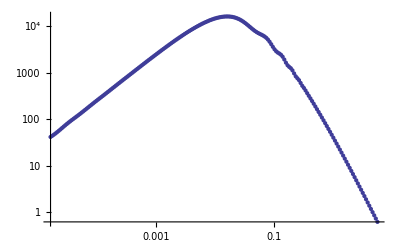

-Graphics-

Export power spectrum raw data

DEs\Sync\PowerSScale.xls

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

DEs\Sync\PowerSDE2.xls

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

DEs\Sync\PowerSDE3.xls

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

DEs\Sync\PowerSDE4.xls

```mathematica
(*********************************************)
Print[Style["Power spectrums for the models. This is a slow method to calculate the power spectrums but it's steady.",Orange]]
(*********************************************)
(*
PowerSDE2=Table[{PowerS[[i,1]]/h,(frac2 (GrowthDE2[1]/GrowthDE2[aokTabDE2[[i]][[1]]])/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]]))^2 PowerS[[i,2]] h^3},{i,1,leth-tranzDE2}];
PowerSDE3=Table[{PowerS[[i,1]]/h,(frac3 (GrowthDE3[1]/GrowthDE3[aokTabDE3[[i]][[1]]])/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]]))^2 PowerS[[i,2]] h^3},{i,1,leth-tranzDE3}];
PowerSDE4=Table[{PowerS[[i,1]]/h,(frac4 (GrowthDE4[1]/GrowthDE4[aokTabDE4[[i]][[1]]])/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]]))^2 PowerS[[i,2]] h^3},{i,1,leth-tranzDE4}];
*)
 (*It should be faster but it sucks.*)
(*********************************************)
Print[Style["Construct the normalized power spectrum (different units) and export them",Orange]]
(*********************************************)
PowerSS=Table[{PowerS[[i,1]],PowerS[[i,2]]},{i,1,leth}];
PowerSDE2=Table[{PowerSS[[i,1]],(Qfac2[[i]][[2]])^2 PowerSS[[i,2]]},{i,1,leth}];
PowerSDE3=Table[{PowerSS[[i,1]],(Qfac3[[i]][[2]])^2 PowerSS[[i,2]]},{i,1,leth}];
PowerSDE4=Table[{PowerSS[[i,1]],(Qfac4[[i]][[2]])^2 PowerSS[[i,2]]},{i,1,leth}];
ListLogLogPlot[PowerS]
ListLogLogPlot[PowerSS]
(*********************************************)
Print[Style["Export power spectrum raw data",Orange]]
(*********************************************)
Export["DEs\\Sync\\PowerSScale.xls",PowerSS,"XLS"]
Export["DEs\\Sync\\PowerSDE2.xls",PowerSDE2,"XLS"]
Export["DEs\\Sync\\PowerSDE3.xls",PowerSDE3,"XLS"]
Export["DEs\\Sync\\PowerSDE4.xls",PowerSDE4,"XLS"]
```

Import the Q factors calculated previously.

Plot P(k)

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

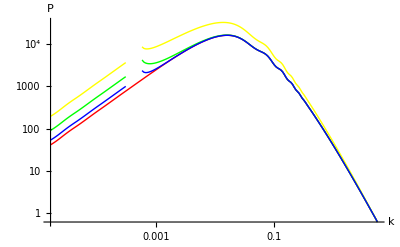

NIntegrate::nlim: x = aL ⟦ 1 ⟧ is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

-Graphics-

Plot Qfactors vs k

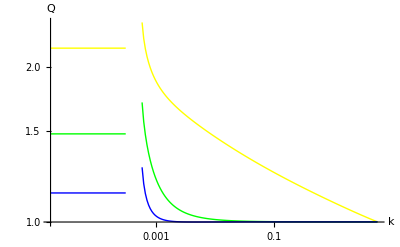

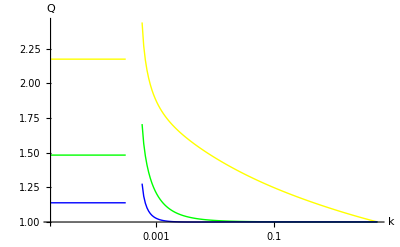

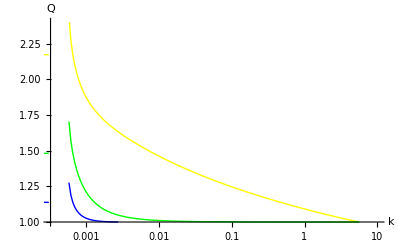

Plot Hubble distances. Normalized.

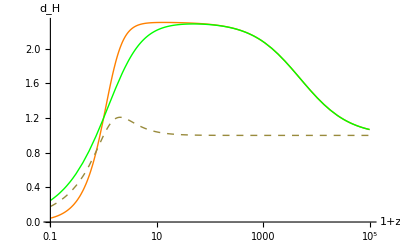

```mathematica
(*********************************************)
Print[Style["Import the Q factors calculated previously.",Orange]]
(*********************************************)
QfDe2VsL=Import["DEs\\Sync\\QfactorDE2vsL.xls"];
QfDe3VsL=Import["DEs\\Sync\\QfactorDE3vsL.xls"];
QfDe4VsL=Import["DEs\\Sync\\QfactorDE4vsL.xls"];
(*********************************************)
Print[Style["Plot P(k)",Orange]]
(*********************************************)
ListLogLogPlot[{PowerSS,PowerSDE2,PowerSDE3,PowerSDE4},Joined->True,AxesLabel->{k,P},PlotRange->Automatic,PlotStyle->{Red,Yellow,Green,Blue},PlotLegend->{"LCDM","w2","w3","w4"},LegendPosition->{1.1,-0.4}]
ListLogLogPlot[{PowerSS,PowerSDE2,PowerSDE3,PowerSDE4},Joined->True, AxesLabel-> {k,P},PlotRange->Automatic,PlotStyle->{Red,Yellow,Green,Blue},PlotLegend->{"LCDM","w2","w3","w4"},LegendPosition->{1.1,-0.4}]
(*********************************************)
Print[Style["Plot Qfactors vs k",Orange]]
(*********************************************)
ListLogLogPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->Full,PlotStyle->{Yellow,Green,Blue},PlotLegend->{"w2","w3","w4"},LegendPosition->{1.1,-0.4}]
ListLogLinearPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->Full,PlotStyle->{Yellow,Green,Blue},PlotLegend->{"w2","w3","w4"},LegendPosition->{1.1,-0.4}]
ListLogLinearPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->{{3.3*10^-4,10},{1,2.4}},PlotStyle->{Yellow,Green,Blue},PlotLegend->{"w2","w3","w4"},LegendPosition->{1.1,-0.4}]
(*Table[NSolve[PowerS[[i,1]]== H2[a2] && a2>0,a2,Reals],{i,1,Length[PowerS]}]*)
(*(*********************************************)
Print[Style["Plot growth factors of a for all models. Normalized.",Orange]]
(*********************************************)
LogLogPlot[{fracs mn GS[mn],mn GL[mn],frac2 mn GDE2[mn],frac3 mn GDE3[mn],frac4 mn GDE4[mn]},{mn,0.1,1000},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {1+z,"D_+(1+z)"},PlotLegend->{"sCDM","LCDM","w2","w3","w4"},LegendPosition->{1.1,-0.4}]
LogLogPlot[{mn GL[mn],mn frac3 GDE3[mn]},{mn,0.1,100},PlotStyle->{Orange,Green},AxesLabel->{"1+z","D_+(z)(1+z)"},PlotLegend->{"LCDM","DE3"},LegendPosition->{1.1,-0.4}]
LogLogPlot[{GS[mn]/GS[mn],GL[mn]/(fracs GS[mn]),(frac2 GDE2[mn])/(fracs GS[mn]),(frac3 GDE3[mn])/(fracs GS[mn]),(frac4 GDE4[mn])/(fracs GS[mn])},{mn,0.1,1000},PlotStyle->{Red,Orange,Yellow,Green,Blue},AxesLabel-> {"1+z","D_+(z)(1+z)"},PlotLegend->{"sCDM","LCDM","DE2","DE3","DE4"},LegendPosition->{1.1,-0.4}]*)
(*********************************************)
Print[Style["Plot Hubble distances. Normalized.",Orange]]
(*********************************************)
LogLinearPlot[{LambdaL[mn]/Lambdas[mn],Lambda3[mn]/Lambdas[mn],LambdaL[mn]/Lambda3[mn]},{mn,0.1,10^5},PlotStyle->{Orange,Green,Dashed},AxesLabel->{"1+z","d_H"},PlotLegend->{"L/s","DE3/s","L/DE3"},LegendPosition->{1.1,-0.4}]
```